(1.0f + (cosf(0.2f*x)/sqrtf(fabsf(x+12.f)+1.f)))*(x/6.f - 3.f)*(x/6.f - 3.f) -
                sqrtf(fabsf(0.5f*x + 1.f))

```mathematica
f[x_]=-√Abs[1+x/2]+(-3+x/6)^2 (1+Cos[0.2x]/(√(1+Abs[12+x])))
```

-√Abs[1+x/2]+(-3+x/6)^2 (1+Cos[0.2 x]/(√(1+Abs[12+x])))

```mathematica
xv={-42.,-35.,-16.,-8.,-3.,-2.5,0.,0.5,4.0,8.5,22.,33.,45.,48.,55.};
Map[f,xv]//N
```

{86.2012,85.9734,15.1293,16.8005,14.7401,14.3352,10.4962,9.69264,4.63238,0.145995,-3.04275,2.94235,12.9797,16.8481,32.7096}

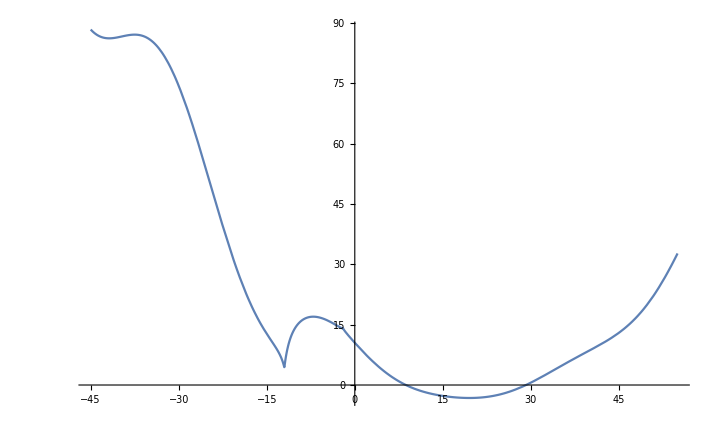

```mathematica
Plot[f[x],{x,-45,55}]
```

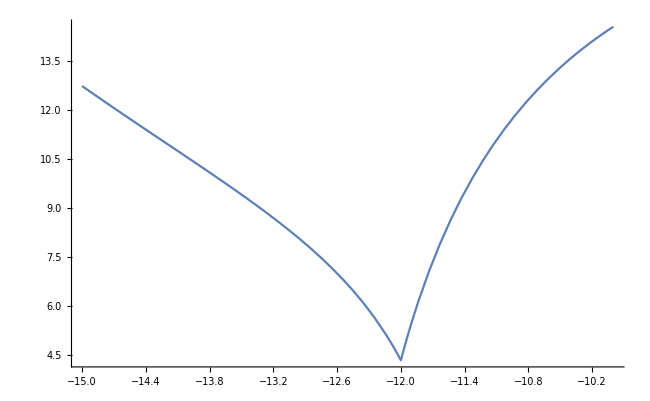

```mathematica
Plot[f[x],{x,-15,-10}]
```

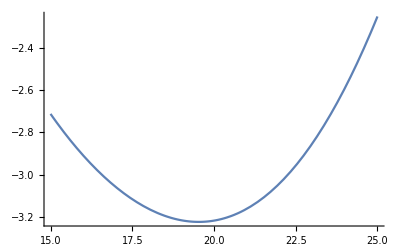

```mathematica
Plot[f[x],{x,15,25}]
```